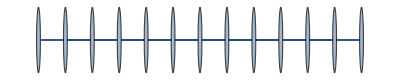

```mathematica
Graph[JacobsThalGraph[9],GraphLayout->"GridEmbedding"]
```

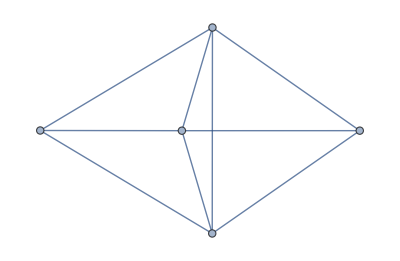

```mathematica
ReadGrof[2]
```

```mathematica
With[{min=9000,max=9100},
Monitor[Table[HasFullProperty[ReadGrof[kk]],{kk,min,max}],Row[{kk,ProgressIndicator[(kk-min)/(max-min)],max}]
]
]//Tally
```

{{True,101}}

```mathematica
With[{min=109000,max=109100},
Monitor[Table[HasFullProperty[ReadGrof[kk]],{kk,min,max}],Row[{kk,ProgressIndicator[(kk-min)/(max-min)],max}]
]
]//Tally
```

{{True,101}}

```mathematica
With[{min=309000,max=309100},
Monitor[Table[HasFullProperty[ReadGrof[kk]],{kk,min,max}],Row[{kk,ProgressIndicator[(kk-min)/(max-min)],max}]
]
]//Tally
```

{{True,101}}

```mathematica
EdgeCount[GraphComplement[ReadGrof[398438]]]
```

55

```mathematica
FactorInteger[55]
```

{{5,1},{11,1}}

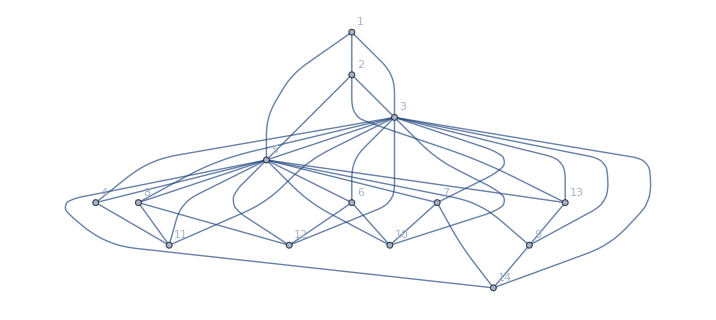

```mathematica
Graph[ReadGrof[398438], GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name"]
```

```mathematica
ChromaticPolynomial[ReadGrof[398438], 4]
```

24

```mathematica
Map[SymbolToLabel,FindFullFormula4[ReadGrof[398438]]]
```

{1abcde♁246789♁3♁5}

```mathematica
With[{min=398438-1000+1,max=398438},
Monitor[Table[HasFullProperty[ReadGrof[kk]],{kk,min,max}],Row[{kk,ProgressIndicator[(kk-min)/(max-min)],max}]
]
]//Tally
```

{{True,1000}}

```mathematica
Fold[And,Out[362]]
```

True

```mathematica
HasFullProperty[ReadGrof[100]]
```

False

```mathematica
With[{g=ReadGrof[100]},Table[HasProperty[g,k],{k,5,VertexCount[g]}]]
```

{True,True,True,True,True,True}